# Analysis code for error vs. complexity test

Right now, this code is set up to analyze spherical data, and should work with only a change to the filename within sphereData and changes to the filenames for the spheres within sphere import & area evaluation. Additional helper functions are included in case one wants to try a version of this test for a surface that requires numerically integrated geodesics, although the inherent error in the numerical integration & potentially misdirected geodesics can be misleading (as the current code only implements a straightness criterion for the geodesic, rather than straightest & shortest).

## Preliminaries

### Data Import

```mathematica
sphereData=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\data\\error_v_complexity\\200_sphere_error_v_complexity_final.csv","Data"] (*or wherever your err_v_complexity output is*);
(*torusData=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\data\\error_v_complexity\\torus_error_v_complexity.csv","Data"];*)
```

### Helper Functions

```mathematica
(*extra functions in case one wants to attempt NDSolve requiring surfaces*)
d=2;c=3; a=1;R=1;(*torus major and minor radii, sphere radius*)
```

```mathematica
torusSurfacePos[u_,v_]:={(c+a*Cos[v])Cos[u],(c+a*Cos[v])Sin[u],a*Sin[v]}
sphereSurfacePos[θ_,ϕ_]:=R*{Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ], Cos[θ]}
```

```mathematica
generatePrimitives[u_,v_,surfacePos_]:=Module[{udot,vdot,cs,cdots,uode,vode, g, gInverse,christoffelSymbols},
udot = D[u,t];
vdot = D[v,t];
cs={u,v};
cdots = {udot,vdot};
g =FullSimplify[ ({{D[surfacePos[u,v],u].D[surfacePos[u,v],u], D[surfacePos[u,v],u].D[surfacePos[u,v],v]}, {D[surfacePos[u,v],v].D[surfacePos[u,v],u], D[surfacePos[u,v],v].D[surfacePos[u,v],v]}})];
gInverse = FullSimplify[Inverse[g]];
christoffelSymbols[k_,i_,j_] := ∑_(m=1)^d (1/2)*Part[gInverse,k,m] *(D[Part[g,i,m],Part[cs,j]] + D[Part[g,j,m],Part[cs,i]] - D[Part[g,i,j],Part[cs,m]]);
uode=FullSimplify[ D[cdots[[1]],t] + ∑_(i=1)^2 ∑_(j=1)^2 christoffelSymbols[1,i,j]*cdots[[i]]*cdots[[j]]==0];
vode =FullSimplify[ D[cdots[[2]],t]+ ∑_(i=1)^2 ∑_(j=1)^2 christoffelSymbols[2,i,j]*cdots[[i]]*cdots[[j]]==0];
{uode,vode,g}
]
```

```mathematica
{tode,pode,gSphere} = generatePrimitives[θ[t],ϕ[t], sphereSurfacePos];
{uode,vode,gTorus} = generatePrimitives[u[t],v[t],torusSurfacePos];
```

```mathematica
σ[tf_?NumericQ,path_,u_,v_,g_]:=Module[{cs},
cs ={u,v};
NIntegrate[Sqrt[Evaluate[g[[1,1]]/.path]*Evaluate[D[cs[[1]]/.path,t]]^2 +2*Evaluate[g[[2,1]]/.path]*Evaluate[D[cs[[1]]/.path,t]]*Evaluate[D[cs[[2]]/.path,t]] +
Evaluate[g[[2,2]]/.path]*Evaluate[D[cs[[2]]/.path,t]^2]],{t,0,tf}]
]
```

```mathematica
xyFromuv[eps_]:= Module[{u1,v1, u2,v2},
u1 = eps[[1]];v1 = eps[[2]];
torusSurfacePos[u1,v1]
]
```

```mathematica
uvFromxy[p_]:= Module[{x1,y1,z1},
(*r1 r2 are spatial rescalings that we can ignore when not trying to compare distances*)
x1 = p[[1]];y1 = p[[2]];z1 = p[[3]];
{ArcTan[x1,y1],ArcTan[√(x1^2+y1^2)-c,z1]}
]
θϕFromxy[p_]:=Module[{x1,y1,z1},
x1 = p[[1]];y1 = p[[2]];z1 = p[[3]];
{ArcTan[z1,√(x1^2+y1^2)],ArcTan[x1,y1]}
]
```

```mathematica
uvFromxyPair[eps_]:= Module[{x1,y1,z1,x2,y2,z2},
x1 = eps[[1,1]];y1 = eps[[1,2]];z1 = eps[[1,3]];x2 = eps[[2,1]];y2 = eps[[2,2]];z2 = eps[[2,3]];
{{ArcTan[x1,y1],ArcTan[√(x1^2+y1^2)-c,z1]},{ArcTan[x2,y2],ArcTan[√(x2^2+y2^2)-c,z2]}}
]
```

```mathematica
(*we need to make the xyz tangent, rather than the uv tangent*)
getDistanceTorus[tf_,endpoint_]:=Module[{u1,v1,u2,v2,bcs,pathToRead},
u1 = endpoint[[1,1]];v1 =endpoint[[1,2]];u2 = endpoint[[2,1]]; v2 = endpoint[[2,2]];
(*reversing order to get path tangent at source point specifically*);
bcs = {u[tf] ==u1, v[tf]==v1,u[0]==u2,v[0]==v2};
pathToRead=NDSolve[{uode,vode,bcs},{u[t],v[t]},{t,0,tf}];
σ[tf,pathToRead,u[t],v[t],gTorus][[1]]
]
getDistancesTorus[tf_,eplist_]:=Table[getDistanceTorus[tf,eplist[[i]]],{i,Length[eplist]}]
makePathTangentTorus[tf_,endpoint_]:=Module[{bcs,pathToRead,u1,v1,u2,v2,uvTangent, δx, δy, δz},
u1 = endpoint[[1,1]];v1 =endpoint[[1,2]];u2 = endpoint[[2,1]]; v2 = endpoint[[2,2]];
(*reversing order to get path tangent at source point specifically*);
bcs = {u[tf] ==u1, v[tf]==v1,u[0]==u2,v[0]==v2};
pathToRead=NDSolve[{uode,vode,bcs},{u[t],v[t]},{t,0,tf}];
uvTangent=Flatten[D[{u[t],v[t]}/.pathToRead,t]/.t->tf];
(*round off to remove numerical errors -- we know that the answer is (-1/2, 0) for all of these, see below*);
uvTangent = {Round[uvTangent[[1]],10^(-4)],Round[uvTangent[[2]],10^(-4)]};
δx =-a*Sin[v1]*Cos[u1]*uvTangent[[2]] - ((c+a*Cos[v1])*Sin[u1])*uvTangent[[1]];
δy = -a*Sin[v1]*Sin[u1]*uvTangent[[2]] +((c+a*Cos[v1])*Cos[u1])*uvTangent[[1]];
δz = a*Cos[v1]*uvTangent[[2]];
{δx,δy,δz}
]
makePathTangentsTorus[tf_,epList_]:= Table[makePathTangentTorus[tf,epList[[i]]],{i,1,Length[epList]}]
```

```mathematica
(*we need to make the xyz tangent, rather than the uv tangent*)
getDistanceSphere[tf_,endpoint_]:=Module[{u1,v1,u2,v2,bcs,pathToRead},
u1 = endpoint[[1,1]];v1 =endpoint[[1,2]];u2 = endpoint[[2,1]]; v2 = endpoint[[2,2]];
(*reversing order to get path tangent at source point specifically*);
bcs = {θ[tf] ==u1, ϕ[tf]==v1,θ[0]==u2,ϕ[0]==v2};
pathToRead=NDSolve[{tode,pode,bcs},{θ[t],ϕ[t]},{t,0,tf}];
σ[tf,pathToRead,θ[t],ϕ[t],gSphere][[1]]
]
getDistancesSphere[tf_,eplist_]:=Table[getDistanceSphere[tf,eplist[[i]]],{i,Length[eplist]}]
makePathTangentSphere[tf_,endpoint_]:=Module[{bcs,pathToRead,u1,v1,u2,v2,uvTangent, δx, δy, δz},
u1 = endpoint[[1,1]];v1 =endpoint[[1,2]];u2 = endpoint[[2,1]]; v2 = endpoint[[2,2]];
(*reversing order to get path tangent at source point specifically*);
bcs = {θ[tf] ==u1, ϕ[tf]==v1,θ[0]==u2,ϕ[0]==v2};
pathToRead=NDSolve[{tode,pode,bcs},{θ[t],ϕ[t]},{t,0,tf}];
uvTangent=Flatten[D[{θ[t],ϕ[t]}/.pathToRead,t]/.t->tf];
(*round off to remove numerical errors -- we know that the answer is (-1/2, 0) for all of these, see below*);
uvTangent = {Round[uvTangent[[1]],10^(-4)],Round[uvTangent[[2]],10^(-4)]};
δx = Cos[u1] Cos[v1] uvTangent[[1]]-Sin[u1] Sin[v1] uvTangent[[2]];
δy =Cos[u1] Sin[v1] uvTangent[[1]]+Cos[v1] Sin[u1] uvTangent[[2]];
δz =-Sin[u1] uvTangent[[1]];
{δx,δy,δz}
]
makePathTangentsSphere[tf_,epList_]:= Table[makePathTangentSphere[tf,epList[[i]]],{i,1,Length[epList]}]
```

```mathematica
(*key functions for the plot in the paper -- get the tangent to the great circle at a point given another point along its line & get how far we would have gone on a great circle with a given heading + distance*)
greatCircleTangent[p1_,p2_]:=Module[{u,w,v},
(*tangent at p1, given p2; assumes sphere is radius 1*)
u = Normalize[p1];
w = Normalize[Cross[p1,p2]];
v = Normalize[Cross[u,w]]
]
greatCircleDisplacement[p1_, dis_, disLength_]:=Module[{u,v,ndis, dω,pNewForward,pNewBackward},
(*determine what great circle we're on with p1 and (from cSS) dis, then move a certain amount of arc length along it. Normalize calls are safety guards.*)
u = Normalize[p1];
ndis = Normalize[dis];
v = Normalize[ndis-Dot[u,ndis]*u] (*guarantees u and v are an orthonormal basis*);
dω = disLength (*Because dtheta = arc length/R, and R = 1*);
pNewForward = u*Cos[dω]+v*Sin[dω];  
pNewBackward = u*Cos[dω]-v*Sin[dω];
{pNewForward, pNewBackward} (*return both because we don't a priori know if we've guessed the right direction, but it will be very obvious on comparison*)
]
```

```mathematica
standardError[ds_]:=StandardDeviation[ds]/Sqrt[Length[ds]];
```

```mathematica
tSurf=ParametricPlot3D[torusSurfacePos[u,v],{u,0,2π},{v,-π,π}];
sSurf=ParametricPlot3D[sphereSurfacePos[u,v],{u,0,π},{v,-π,π},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

## Analysis

```mathematica
(*guide to data is: complexity, p1x, p1y, p1z, p2x, p2y, p2z, distance, tangentx, tangenty, tangentz, displacementheadingx, displacementheadingy, displacementheadingz, largedisplacedx, largedisplacedy, largedisplacedz, smalldisplacedx, smalldisplacedy, smalldisplacedz; total 20 entries.*)
```

### Complexity data deconstruction & analysis

```mathematica
(*sphere*)
sC = Table[sphereData[[i,1]],{i,Length[sphereData]}];
sP1=Table[sphereData[[i]][[{2,3,4}]],{i,Length[sphereData]}];
sP2 = Table[sphereData[[i]][[{5,6,7}]],{i,Length[sphereData]}];
(*comparison*)
sD = Table[sphereData[[i,8]],{i,Length[sphereData]}];
sT  = Table[sphereData[[i]][[{9,10,11}]],{i,Length[sphereData]}];
sF = Table[sphereData[[i]][[{12,13,14}]],{i,Length[sphereData]}];
sdLarge = Table[sphereData[[i]][[{15,16,17}]],{i,Length[sphereData]}];
sdSmall = Table[sphereData[[i]][[{18,19,20}]],{i,Length[sphereData]}];
lMag = 0.5;
sMag = 0.05;
```

```mathematica
sUVs = Table[{θϕFromxy[sP1[[i]]],θϕFromxy[sP2[[i]]]},{i,Length[sphereData]}];
```

```mathematica
nAverage = 200;
sComplexities = Table[Mean[Partition[sC,nAverage][[i]]],{i,Length[Partition[sC,nAverage]]}]
```

{122,272,482,752,1472,2432,3632,5882,7682,9722,14522,20282}

```mathematica
(*distance*)
analyticSDist = Table[SphericalDistance[sUVs[[i,1]],sUVs[[i,2]]],{i,Length[sphereData]}];
sErrors =Table[analyticSDist[[i]]-sD[[i]],{i,Length[sphereData]}];
groupedSErrors = Partition[sErrors,nAverage];
averageSErrors = Table[Mean[groupedSErrors[[i]]],{i,Length[groupedSErrors]}];
distErrorsComplexities = Table[{sComplexities[[i]],averageSErrors[[i]]},{i,Length[sComplexities]}]
```

{{122,0.0202805},{272,0.00869428},{482,0.00523522},{752,0.00321428},{1472,0.00164205},{2432,0.000986395},{3632,0.000675798},{5882,0.000424209},{7682,0.000321646},{9722,0.000246641},{14522,0.000167929},{20282,0.000114628}}

```mathematica
(*tangents*)
sphGCTangents = Table[greatCircleTangent[sP1[[i]],sP2[[i]]],{i,Length[sP1]}];
partitionedTangError = Partition[Table[1-Abs[Dot[sphGCTangents[[i]],sT[[i]]]],{i,Length[sT]}],nAverage];
meanTangErrors = Table[{sComplexities[[i]],Mean[partitionedTangError[[i]]]},{i,Length[partitionedTangError]}];
stdErrTangErrors = Table[{sComplexities[[i]],standardError[partitionedTangError[[i]]]},{i,Length[partitionedTangError]}];
varTangErrors = Table[{sComplexities[[i]],Variance[partitionedTangError[[i]]]},{i,Length[partitionedTangError]}];
varDistErrors = Table[Variance[groupedSErrors[[i]]],{i,Length[groupedSErrors]}];
stdErrDistErrors = Table[standardError[groupedSErrors[[i]]],{i,Length[groupedSErrors]}];
```

```mathematica
(*displacements*)
largeDispTable = Table[greatCircleDisplacement[sP1[[i]], sF[[i]], lMag],{i,Length[sP1]}] (*returns both forward and backward displacement points along great circle from p1*);
smallDispTable = Table[greatCircleDisplacement[sP1[[i]], sF[[i]], sMag],{i,Length[sP1]}] (*returns both forward and backward displacement points along great circle from p1*);
(*now -- calculate error from both forward and backward, and pick the smaller*)
largeDispErrors = Table[1-Max[Dot[sdLarge[[i]],largeDispTable[[i,1]]], Dot[sdLarge[[i]],largeDispTable[[i,2]]]],{i,Length[sdLarge]}];
smallDispErrors = Table[1-Max[Dot[sdSmall[[i]],smallDispTable[[i,1]]], Dot[sdSmall[[i]],smallDispTable[[i,2]]]],{i,Length[sdSmall]}];
```

```mathematica
groupedLDisp=Partition[largeDispErrors,nAverage];
meanLDispErrors = Table[Mean[groupedLDisp[[i]]],{i,Length[groupedLDisp]}];
stdLDispErrors = Table[standardError[groupedLDisp[[i]]],{i,Length[groupedLDisp]}];
groupedSDisp=Partition[smallDispErrors,nAverage];
meanSDispErrors = Table[Mean[groupedSDisp[[i]]],{i,Length[groupedSDisp]}];
stdSDispErrors = Table[standardError[groupedSDisp[[i]]],{i,Length[groupedSDisp]}];
```

```mathematica
tangChartData=Table[{sqrtTriAreas[[i]],meanTangErrors[[i,2]]},{i,1,Length[sComplexities]}];
distChartData=Table[{sqrtTriAreas[[i]],averageSErrors[[i]]},{i,1,Length[sComplexities]}];
lDispChartData = Table[{sqrtTriAreas[[i]],meanLDispErrors[[i]]},{i,1,Length[sComplexities]}];
sDispChartData = Table[{sqrtTriAreas[[i]],meanSDispErrors[[i]]},{i,1,Length[sComplexities]}];
tangChartDataWBars=Table[{sComplexities[[i]],Around[meanTangErrors[[i,2]],stdErrTangErrors[[i,2]]]},{i,1,Length[sComplexities]}];
distChartDataWBars=Table[{sComplexities[[i]],Around[averageSErrors[[i]],stdErrDistErrors[[i]]]},{i,1,Length[sComplexities]}];
lDispChartDataWBars = Table[{sComplexities[[i]],Around[meanLDispErrors[[i]],stdLDispErrors[[i]]]},{i,1,Length[sComplexities]}];
sDispChartDataWBars = Table[{sComplexities[[i]],Around[meanSDispErrors[[i]],stdSDispErrors[[i]]]},{i,1,Length[sComplexities]}];
```

Part::partd: Part specification sqrtTriAreas⟦1⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦2⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification sqrtTriAreas⟦1⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦2⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification sqrtTriAreas⟦1⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦2⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification sqrtTriAreas⟦1⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦2⟧ is longer than depth of object.

Part::partd: Part specification sqrtTriAreas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### Sphere import & area evaluation

```mathematica
(*these filenames also all need to be changed to wherever you store your sphere meshes -- you can also generate them with the commented example code below*)
sm1=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_1.off","MeshRegion"];
sm2=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_2.off","MeshRegion"];
sm3=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_3.off","MeshRegion"];
sm4=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_4.off","MeshRegion"];
sm5=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_5.off","MeshRegion"];sm6=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_6.off","MeshRegion"];
sm7=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_7.off","MeshRegion"];
sm8=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_8.off","MeshRegion"];
sm9=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_9.off","MeshRegion"];
sm10=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_10.off","MeshRegion"];
sm11=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_11.off","MeshRegion"];sm12=Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphere_mesh_12.off","MeshRegion"];
spheres = {sm1, sm2, sm3, sm4, sm5, sm6, sm7, sm8, sm9, sm10, sm11, sm12};
sqrtTriAreas = Table[Sqrt[Area[spheres[[i]]]/Length[MeshCells[spheres[[i]],2]]],{i,Length[spheres]}]
invSqrtTriAreas = Table[1/sqrtTriAreas[[i]],{i,Length[spheres]}]
```

{0.225965,0.151694,0.11405,0.0913437,0.0653103,0.0508177,0.0415867,0.0326805,0.0285972,0.0254208,0.0207999,0.0176004}

{4.42546,6.59222,8.76811,10.9477,15.3115,19.6782,24.0462,30.5993,34.9685,39.3379,48.0772,56.8168}

### Final plot using sphere triangle areas/analysis

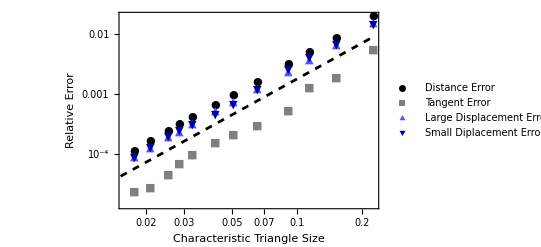

```mathematica
Oh2 = Table[{x,x^2},{x, 0,0.23,0.001}];
mainData=ListLogLogPlot[{distChartData,tangChartData,lDispChartData,sDispChartData},LabelStyle->{Black,FontSize->16},PlotMarkers->{"●","■","▲","▼"},PlotStyle->{Black,Gray, Lighter[Blue],Darker[Blue]},Frame->True,PlotLegends->{"Distance Error","Tangent Error","Large Displacement Error", "Small Diplacement Error"},FrameLabel->{"Characteristic Triangle Size","Relative Error"}];
Oh2Cont = LogLogPlot[.18*(x)^2,{x,0,0.23},PlotStyle->{Black,Dashed}];
Show[mainData,Oh2Cont]
```

## bonus example code for making meshes, working on tori

```mathematica
(*drSph=DiscretizeRegion[Sphere[],PrecisionGoal->1,MaxCellMeasure->0.000003,MeshCellStyle->{{2,All}->None,{1,All}->Black}];
Export["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\paper1_curved_space\\meshes\\mathematica_spheres\\sphereMeasure3e6.off",drSph,"BinaryFormat"->False]*)
```

```mathematica
(*
(*tangents -- wrapping below in quiet while noting that any two points that are nearly antipodal will cause issues*)
sphAnalyticTangents = Quiet[makePathTangentsSphere[2,sUVs]];
(*similarly, wrapping the below in quiet but note that six data points have to be deleted for being antipodal -- I'm sure there's a more automatic way to do it than checking each entry and deleting anything that isn't a number by hand*)
normedSphAnalyticTangents = Quiet[Table[Normalize[sphAnalyticTangents[[i]]],{i,Length[sphAnalyticTangents]}]];
tangError = Quiet[Table[1-Abs[Dot[normedSphAnalyticTangents[[i]],sT[[i]]]],{i,Length[sT]}]];
partitionedTangError =Partition[tangError,100];
partitionedTangError[[3]] =Delete[Sort[partitionedTangError[[3]]],100];
partitionedTangError[[6]]=Delete[Sort[partitionedTangError[[6]]],100];
partitionedTangError[[7]]=Delete[Sort[partitionedTangError[[7]]],100];
partitionedTangError[[8]]=Delete[Sort[partitionedTangError[[8]]],100];
partitionedTangError[[9]]=Delete[Sort[partitionedTangError[[9]]],100];
partitionedTangError[[12]]=Delete[Sort[partitionedTangError[[12]]],100];*)
```

```mathematica
(*dP1 = *)
(*
(*torus*)
tC = Table[torusData[[i,1]],{i,Length[torusData]}];
tP1=Table[torusData[[i]][[{2,3,4}]],{i,Length[torusData]}];
tP2 = Table[torusData[[i]][[{5,6,7}]],{i,Length[torusData]}];
(*comparison*)
tD = Table[torusData[[i,8]],{i,Length[torusData]}];
tT  = Table[torusData[[i]][[{9,10,11}]],{i,Length[torusData]}];
tF = Table[torusData[[i]][[{12,13,14}]],{i,Length[torusData]}];*)
(*tUVs = Table[{uvFromxy[tP1[[i]]],uvFromxy[tP2[[i]]]},{i,Length[torusData]}]*)
```